```mathematica
Module[{a=158.4,b=0.288,c,d,e},NonlinearModelFit[data,Re[{c/(1+Exp[d-Log[a/(b* x)-1/b]/e])}],{{d,2.6},{c,160},{e,0.45}},x]]
```

FittedModel[157.671 Re[1/(1+(2.51409×10^-11)/(-«19»+«1»)^(«19»))]]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.86541 | 0.00671328 | 724.745 | 9.49225×10^-14
x | 0.674422 | 0.12464 | 5.41096 | 0.0029163

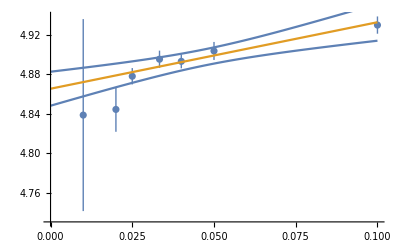

```mathematica
data={{{1/10,4.92997},ErrorBar[0.00875039]},{{1/20,4.90374},ErrorBar[0.00912412]},{{1/25,4.89318},ErrorBar[0.00707122]},{{1/30,4.89534},ErrorBar[0.00870608]},{{1/40,4.87807},ErrorBar[0.00829155]},{{1/50,4.84442},ErrorBar[0.0226886]},{{1/100,4.83867},ErrorBar[0.0973819]}};
error=data[[All,2]]/.ErrorBar[x_]->x;
t=Table[{data[[i,1,1]],Around[data[[i,1,2]],error[[i]]]},{i,Length[error]}];
lmf=LinearModelFit[data[[All,1]],x,x,Weights->1/error^2];
lmf["ParameterTable"]
Show[ListPlot[t],Plot[{lmf["MeanPredictionBands"],lmf[x]},{x,0,0.1}]]
```

```mathematica
Import[]
```